```mathematica
Clear["Global`*"]
```

# Bayesian Model of distance perception from ocular convergence

## Peter Scarfe and Paul Hibbard (2025)

## Main code file for the derivation of the model

## Variables we will be using

### These are just a bunch of setup variables

```mathematica
(* Trigger saving or not *)
doSaving=False;
```

```mathematica
(* Trigger saving or not *)
titlePaddingValue=10;
```

```mathematica
(* Can use Mathstatica or an alternative method *)
useMathstatica=True;
```

```mathematica
(* Distances in cm *)
distanceValues=N@{30, 40, 50, 60, 70, 80, 90, 100};
numDistances=Length[distanceValues];

(* IOD and half IOD *)
iodValue= N@6.5;
hiodValue=iodValue/2;

(* Vergence values (radians and degrees *)
vergValue=ArcTan[hiodValue/distanceValues];
vergDegValue=vergValue/Degree;

(* Sigma values for vergence *)
sigmaValuesRad=N[Range[0.25, 1.75, 0.25]]*Degree;
numSigmaValues=Length[sigmaValuesRad];

(* For the plots in the paper we use a sigma value of 1. There is nothing magical aobut this, simply a value which illustratively shows patterns in the data *)
sigmaValueRad=N[1*Degree];

(* Setup some stuff for the legends *)
legendLabels=Table[Row[{b,"cm"}],{b,Round@distanceValues}];
sigmaLegendLabels=Table[Row[{b, "°"}],{b,N[Range[0.25, 1.75, 0.25]]}];
```

## Simple triangle that represents the geometry of half vergence

### This just shows the basic geometry we are dealing with

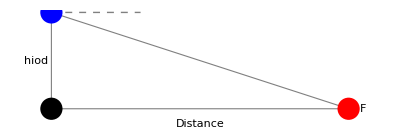

```mathematica
(* Eye, Cyclo and Fix coordinates *)
eyePos={0, hiodValue};
cycloPos={0, 0};
fixPos={ 10, 0};
opticInfPos={3,hiodValue};

(* Graphics bits *)
eye = Graphics[{PointSize[0.04],Blue, Point[eyePos]}];
cyclo = Graphics[{PointSize[0.04],Black,Point[cycloPos]}];
fix =  Graphics[{PointSize[0.04],Red,Point[fixPos]}];

vergTriangle = Graphics[{FaceForm[White], EdgeForm[Directive[Gray]],Triangle[{eyePos,cycloPos,fixPos}]}];
opticInf=Graphics[{Directive[Dashed,Gray],Line[{eyePos,opticInfPos}]}];

theText=Graphics[{
Text["hiod",{-0.5,hiodValue/2}],
Text["Distance",{10/2,-0.5}],
Text["F",{10.5,0}],
}];

(* Show stuff *)
Show[vergTriangle,opticInf,eye,cyclo,fix,theText]
```

#### With a very small distance value the vergence angle approaches Pi/2 i.e., eyes are pointing directly ahead at optical infinity. That is the bounds of the half vergence angle are 0 to Pi/2.

```mathematica
(* Vergence Angle *)
vergAngleTrig=ArcTan[hiodValue/0.00001];
{vergAngleTrig,Pi/2//N}
```

{1.57079,1.5708}

## Probability Density Functions for Vergence

### We assume that the vergence signal is corrupted by zero mean Gaussian noise. However, our vergence distributions are bounded within the interval 0 to Pi / 2, so we need to truncate them. In physical terms this states that (1) negative distances inside or behind the head do not exist, and (2) Distances greater than infinity do not exist.

```mathematica
(* Define our Gaussian for vergence: Using Mathstatica *) 
upperVergLimit=Pi/2;
lowerVergLimit=0;
```

```mathematica
(* Define our Gaussian for vergence: Using Mathstatica *) 
vergFullPDF=PDF[NormalDistribution[m,s],x] ;

(* The domain of f *)
domain[vergFullPDF]={x,lowerVergLimit,upperVergLimit}&&{m∈Reals,h>0,s>0};

(* Define our Gaussian CDF vergence *) 
vergFullCDF[x_] = Prob[x,vergFullPDF];
```

```mathematica
(* Truncate our Gaussian distribution *) 
vergTruncPDF=vergFullPDF/(vergFullCDF[upperVergLimit]-vergFullCDF[lowerVergLimit]);
vergTruncPDF=FullSimplify[vergTruncPDF]

(* Specify the domain and state some assumtions *)
domain[vergTruncPDF]={x,-lowerVergLimit,upperVergLimit}&&{m∈Reals,h>0,s>0};

(* Set up as a function *)
vFunc[m_, s_]=vergTruncPDF;
```

(ⅇ^(-(m-x)^2/(2 s^2)) √(2/π))/(s (Erf[m/(√2 s)]+Erf[(-2 m+π)/(2 √2 s)]))

```mathematica
(* Save the distance PDF Equation out for use with other notebooks *)
If[doSaving,Export[NotebookDirectory[]<>"vergencePDF.mx",vergTruncPDF]];
```

### Check that the truncated distribution calculated by Mathstatica is the same as plain Mathematica and that they integrate to 1

```mathematica
(* Calculate the equation for a truncated distribution via Mathematica alone *)
vergTruncPDFMathAlone=PDF[TruncatedDistribution[{lowerVergLimit,upperVergLimit},NormalDistribution[m,s]],x]//FullSimplify
```

Piecewise[{{(ⅇ^(-(m-x)^2/(2 s^2)) √(2/π))/(s (Erf[m/(√2 s)]-Erf[(m-π/2)/(√2 s)])), x>0&&2 x≤π}, {0, True}}]

```mathematica
(* Varify that this is the same as that generated with Mathstatica *)
True===FullSimplify[vergTruncPDFMathAlone[[1,1,1]]==vergTruncPDF]
```

True

## Expectations for Vergence

### Calculate the expectation (mean) of the truncated vergence PDF’s

```mathematica
(* Expectation: via Mathematica *)
expectVergMathOnly=Expectation[x,x\[Distributed]ProbabilityDistribution[vergTruncPDF,{x,-Infinity,Infinity}],Assumptions->{Reals,m∈Reals,s∈Reals,s>0,m>0}]
```

(2 m)/(Erf[m/(√2 s)]+Erf[(-2 m+π)/(2 √2 s)])

```mathematica
(* Expectation: via Mathstatica *)
p1=vergTruncPDF;
domain[p1] = {x,-Infinity,Infinity}  && {m∈Reals,s>0};
expectFMS=Expect[x,p1]//FullSimplify
```

(2 m)/(Erf[m/(√2 s)]+Erf[(-2 m+π)/(2 √2 s)])

```mathematica
(* They give the same thing *)
expectVergMathOnly==expectFMS
```

True

## Make tables for the vergence distribution PDF and CDFs

```mathematica
(* Table of vergence PDFs *)
vergPDFTable=
ParallelTable[
PDF[
ProbabilityDistribution[vFunc[Part[vergValue, n],sigmaValueRad], {x, lowerVergLimit, upperVergLimit}]
, x]
,{n, 1, numDistances}];
```

```mathematica
(* Table of vergence CDF's *)
vergCDFTable=
ParallelTable[
CDF[
ProbabilityDistribution[vFunc[Part[vergValue, n],sigmaValueRad], {x, lowerVergLimit, upperVergLimit}]
, x]
,{n, 1, numDistances}];
```

### Check that the distributions integrate to 1 over their domain.

```mathematica
ParallelTable[Integrate[vergPDFTable[[n]],{x,lowerVergLimit,upperVergLimit},Assumptions->0<x<Pi/2],{n,1,numDistances}]
```

{1.,1.,1.,1.,1.,1.,1.,1.}

## Use a change of variables to get a distance distribution from vergence

### This is the critical step where we use a transformation of random variables to get condition pdfs for distance from vergence. In a separate file we derive the same thing using plain Mathematica and show that the results are identical.

```mathematica
(* Do the transform *)
distPDF=Transform[y==h/Tan[x], vergTruncPDF];
distPDF=FullSimplify[distPDF]

(* Make a new domain *)
domain[distPDF]=TransformExtremum[y==h/Tan[x], vergTruncPDF]&& {h>0, x>0,h∈Reals,x∈Reals}

(* Create a function *)
distFuncPDF[m_, s_, h_]=distPDF;
```

(ⅇ^(-(m-ArcCot[y/h])^2/(2 s^2)) h √(2/π))/(s (h^2+y^2) (Erf[m/(√2 s)]+Erf[(-2 m+π)/(2 √2 s)]))

{y,0,∞}&&{m∈ℝ,h>0,s>0}&&{h>0,x>0,h∈ℝ,x∈ℝ}

```mathematica
(* Save the distance PDF Equation out for use with other notebooks *)
If[doSaving,Export[NotebookDirectory[]<>"distancePDF.mx",distPDF]];
```

## Get a CDF of these distributions

### Calculate the CDF of the distance PDF’s via Mathstatica and Mathematica and check that the equations are equivalent.

```mathematica
(* CDF via Mathstatica *)
distCDF=Assuming[y>0,Prob[y,distPDF]]
```

(Erf[(-2 m+π)/(2 √2 s)]+Erf[(m-ArcCot[y/h])/(√2 s)])/(Erf[m/(√2 s)]+Erf[(-2 m+π)/(2 √2 s)])

```mathematica
(* CDF via Mathemtica only *)
distCDFMathOnly=Assuming[y>0,CDF[ProbabilityDistribution[distPDF,{y,0,Infinity}],y]]
```

(-Erf[(2 h m-√(h^2) π)/(2 √2 h s)]+Erf[(m-ArcCot[y/h])/(√2 s)])/(Erf[m/(√2 s)]+Erf[(-2 m+π)/(2 √2 s)])

```mathematica
(* Show that they are equaivalent (given that the iod has to be greater than 0) *)
FullSimplify[distCDF==distCDFMathOnly,Assumptions->h>0]
```

True

## Make the tables for the distance probability distributions, PDFs, CDFs and InverseCDFs

```mathematica
(* Make a table of the probability distributions for the full range of distances *)
distLimit=Infinity;
```

```mathematica
(* Make a table of the probability distributions for the full range of distances *)distribTableProb=ParallelTable[ProbabilityDistribution[distFuncPDF[Part[vergValue, n],sigmaValueRad, hiodValue], {y, 0, distLimit}],{n, 1, numDistances}];
```

```mathematica
(* Make a table of the PDF's for the full range of distances *)
distribTablePDF=ParallelTable[Simplify[PDF[distribTableProb[[n]],y],y>0],{n, 1, numDistances}];
```

```mathematica
(* Make a table of the CDF's for the full range of distances *)
distribTableCDF=ParallelTable[Simplify[CDF[distribTableProb[[n]],y],y>0],{n, 1, numDistances}];
```

```mathematica
(* Make a table of the Inverse CDF's for the full range of distances *)
distribTableInverseCDF=ParallelTable[Simplify[InverseCDF[distribTableProb[[n]],y],0<y<1],{n, 1, numDistances}];
```

### Check that the transformed distributions integrate to 1 over their domain.

```mathematica
ParallelTable[Integrate[distribTablePDF[[n]],{y,0,Infinity},Assumptions->y>0],{n,1,numDistances}]
```

{1.,1.,1.,1.,1.,1.,1.,1.}

## Plot the vergence and distance distributions for the paper

Plot the vergence and corresponding distance PDFs.

```mathematica
(* Fonts *)
titleFS=25;
frameFS=18;
insetFS=25;
```

```mathematica
(* Vergence *)
vergPDFPlotPaper=Plot[vergPDFTable, {x,0, 0.2}, 
PlotStyle->Thickness[0.006],
FrameLabel-> {"Vergence (Radians)",TraditionalForm["p"(OverHat[θ]|Subscript[θ, F] )]},
PlotLabel->Style["Probability Density: Vergence",Black,FontSize->titleFS], 
ImageSize->Large, BaseStyle->{FontSize-> 13.5},
FrameStyle->Directive[Black,Thickness[0.0024],FontSize->18],
PlotLegends->Placed[LineLegend[legendLabels,LegendFunction->Framed],{0.86,0.68}], 
Frame->True,ImagePadding->{{Automatic,Automatic},{Automatic,titlePaddingValue}},
PlotRange->{{0,0.2},{0,25}},AspectRatio->0.82,
PlotRangeClipping->False,
Epilog->Inset[Style["(a)",insetFS],Offset[{-1,-1},Scaled[{-0.05,-0.05}]],{Right,Top}]];
```

```mathematica
(* Distance *)
distPDFPlotPaper=Quiet@Plot[distribTablePDF, {y,0, 150}, 
PlotStyle->Thickness[0.006],
FrameLabel-> {"Distance (cm)",TraditionalForm["p"(Subscript[D, F]|OverHat[θ]) ]},
PlotLabel->Style["Probability Density: Distance",Black,FontSize->titleFS], 
ImageSize->Large, BaseStyle->{FontSize-> 13.5},
FrameStyle->Directive[Black,Thickness[0.0024],FontSize->18],
PlotLegends->Placed[LineLegend[legendLabels,LegendFunction->Framed],{0.86,0.68}], 
Frame->True,ImagePadding->{{Automatic,Automatic},{Automatic,titlePaddingValue}},
PlotRange->{{0,150},{0,0.09}},AspectRatio->0.82,
PlotRangeClipping->False,
Epilog->Inset[Style["(b)",insetFS],Offset[{-1,-1},Scaled[{-0.05,-0.05}]],{Right,Top}]];
```

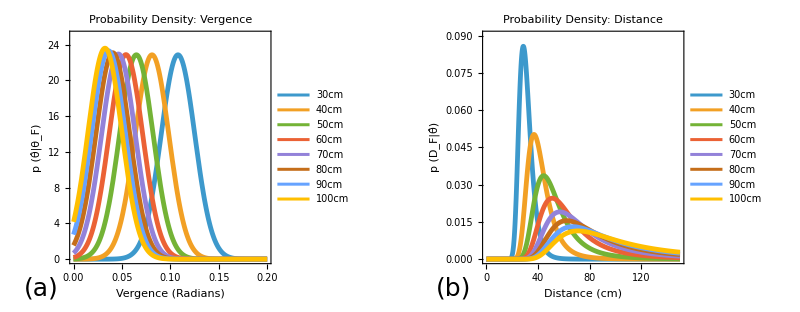

```mathematica
probPlotsPaper=GraphicsRow[{vergPDFPlotPaper,distPDFPlotPaper},ImageSize->Full]
```

```mathematica
(* Save out if we want *)
If[doSaving,Export[StringJoin[NotebookDirectory[],"probPlots.jpeg"],probPlotsPaper, RasterSize->5000,ImageSize->1200]];
```

## Points estimates from the distributions

### Now that we have the probability distributions for distance from vergence we need to make point estimates . To do this we need a cost function . We look at three typical cost functions, (1) quadratic, (2) zero - one and (3) absolute.

#### (1) Quadratic loss function (the mean)

Cannot find a closed form solution for the expectation. So we find a numerical expectation. The bounds for the integration are simply sensible bounds. It does not matter what the upper bound is for the paper, as the mean predicts the opposite pattern to the experimental data. If we chose a larger upper bound for the integration it simply gets more and more disparate from the experimental data.

```mathematica
(* Bounds for the expectation i.e. integration *)
lowerDistLimit=0;
upperDistLimit=600;
```

```mathematica
(* Numerical Expectation *)
theExpectationList=Table[NExpectation[y\[Conditioned]lowerDistLimit<=y<=upperDistLimit,y\[Distributed]distribTableProb[[n]]]-lowerDistLimit,{n, 1, numDistances}];
```

#### (2) Zero-One loss function (the peak)

```mathematica
(* Find the peaks *)
thePeakListFull=Table[FindMaximum[Part[distribTablePDF,n], {y, Part[distanceValues, n]}, Method-> "ConjugateGradient"], {n, Length[distanceValues]}];
```

```mathematica
(* Parse the peaks *)
thePeakList=Part[thePeakListFull, All, 1];
thePeakPosList=Part[thePeakListFull, All, 2, 1,2];
```

### (3) Absolute loss function (the median)

We use the fact that median is the point on the CDF where half of the probability is attained.

```mathematica
theMedianListFull=N[Table[Reduce[Rationalize[distribTableCDF[[n]],0]==1/2&&y>0,y,Reals],{n,1,numDistances}][[All,2]]];
```

Plotting this means that the red dots should lay on the Inverse CDF curves when plotted at the 0.5 probability point.

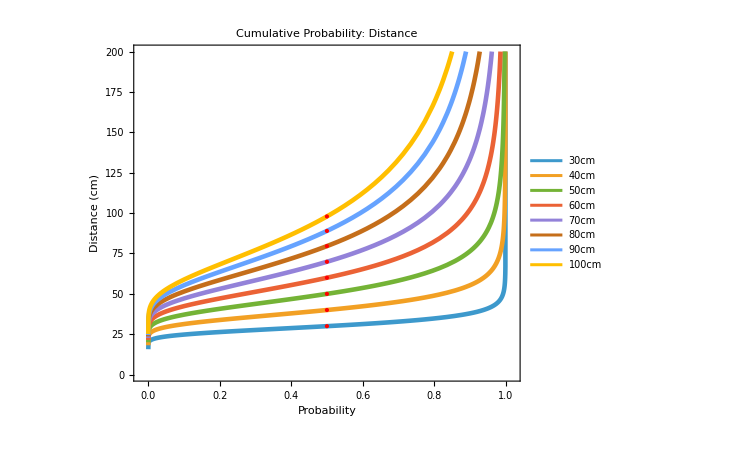

```mathematica
theMedianPos=ConstantArray[0.5,numDistances];
distCDFPlotPaper=Quiet@Plot[distribTableInverseCDF, {y,0, 1}, 
PlotStyle->Thickness[0.006],
FrameLabel-> {"Probability","Distance (cm)"},
PlotLabel->Style["Cumulative Probability: Distance",Black,FontSize->titleFS], 
ImageSize->550, BaseStyle->{FontSize-> 13.5},
FrameStyle->Directive[Black,Thickness[0.0024],FontSize->frameFS],
PlotLegends->Placed[LineLegend[legendLabels,LegendFunction->Framed],{0.13,0.69}], 
Frame->True,ImagePadding->{{Automatic,Automatic},{Automatic,titlePaddingValue}},
PlotRange->{{-0.02,1.02},{0,200}},AspectRatio->0.82,
PlotRangeClipping->False,
Epilog->{{PointSize[Large],Red,Point[Transpose[{theMedianPos, Flatten[theMedianListFull]}]]}
}]
```

```mathematica
If[doSaving,Export[StringJoin[NotebookDirectory[],"distanceCDF.jpeg"],distCDFPlotPaper, RasterSize->5000,ImageSize->1200]];
```

## Peaks, means and medians versus distance: Example

#### Plot of the distance estimates for the three loss functions

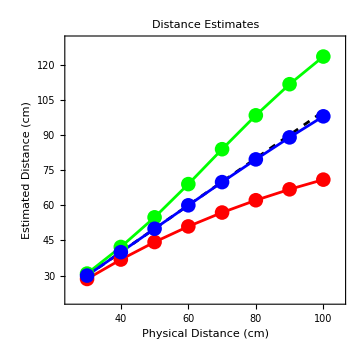

```mathematica
thePlotMarker=Graphics[{Disk[]},ImageSize->15];
ListLinePlot[
{Transpose[{distanceValues,distanceValues}],
Transpose[{distanceValues,thePeakPosList}],
Transpose[{distanceValues,theExpectationList}],
Transpose[{distanceValues,Flatten[theMedianListFull]}]},
AspectRatio->1, 
FrameLabel-> {"Physical Distance (cm)","Estimated Distance (cm)"},PlotLabel->"Distance Estimates",
 BaseStyle->{FontSize-> 14},Frame-> True, ImageSize-> Medium,PlotMarkers->{None,thePlotMarker,thePlotMarker,thePlotMarker},PlotStyle->{{Black,Dashed},Red,Green,Blue},PlotRange->{{25,105},{20,130}}]
```

## Distance peaks for a range of noise levels

### We know that qualitatively choosing the peak predicts the experimental data - here we look at the effect of varying the noise in the vergence signal

```mathematica
(* Distance values for the example plot *)
distanceValues2=N@{20,30, 40, 50, 60, 70, 80, 90, 100};
numDistance2=Length@distanceValues2;
```

```mathematica
(* Convert to vergence values *)
vergValue2=ArcTan[hiodValue/distanceValues2];
numVergValues2=Length@vergValue2;
```

```mathematica
(* Make a table of the distance PDF's for the full range of distances and noise values *)
distribTableSigmas=Table[PDF[ProbabilityDistribution[distFuncPDF[Part[vergValue2, n],Part[sigmaValuesRad,nn], hiodValue], {y, 0, 200}], y],{n, 1, numDistance2},{nn, 1, Length[sigmaValuesRad]}];
```

```mathematica
(* Make a table of the peaks for the distance PDF's *)
thePeakListFullSigmas=Table[FindMaximum[Part[distribTableSigmas,n, nn], {y, Part[distanceValues2, n]}, Method-> "ConjugateGradient"], {n, 1, numVergValues2},{nn, 1, Length[sigmaValuesRad]}];
```

```mathematica
(* Viguier Data *)
vigDataMean={21, 30.5, 37.5, 49.5, 55.5};
vigDataX={20, 30, 40, 60, 80};
vigDataUpper={24, 34.5, 41, 56, 68.5}-vigDataMean;
vigDataLower= vigDataMean-{18, 27, 34, 43, 43};
```

```mathematica
(* Make data and errorbars *)
vigWithError=Table[Around[vigDataMean[[i]],{vigDataLower[[i]],vigDataUpper[[i]]}],{i,1,Length@vigDataMean}];
```

```mathematica
(* Viguier Plot *)
vigData=Transpose[{vigDataX, vigWithError}];
vigDataAll=Transpose[{vigDataX, vigDataMean,vigDataUpper,vigDataLower}];
vigPlot=ListLinePlot[vigData,PlotMarkers->Graphics[Disk[],ImageSize->15], PlotStyle->{Black,Thickness[0.006]},IntervalMarkersStyle->{Black,Thickness[0.005]}];
```

```mathematica
(* Viguier Plot unity line *)
unityLineVig=ListLinePlot[Transpose[{distanceValues2,distanceValues2}],PlotRange->{{10,110},{10,110}},PlotStyle->{Black, Dashed,Thickness[0.006]}];
```

```mathematica
(* Compiale the x-y data for the plotting *)
theFullPos=Join[{distanceValues2},Transpose[Part[thePeakListFullSigmas, All, All,2,1,2]]];
theFullPosData=Transpose[{theFullPos[[1]],#}]&/@theFullPos[[2;;]];
```

```mathematica
mutliNoisePlot=ListLinePlot[theFullPosData,PlotRange->{{15,105},{15,105}},
PlotStyle->Thickness[0.006],PlotMarkers->Graphics[Disk[],ImageSize->15],
AspectRatio->1,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.0024],FontSize->frameFS],
FrameLabel-> {"Physical Distance (cm)","Estimated Distance (cm)"},
PlotLabel->Style["MLE Distance Estimates",Black,FontSize->titleFS],
BaseStyle->{FontSize-> 16},PlotLegends->Placed[LineLegend[sigmaLegendLabels,LegendFunction->Framed],{0.135,0.72}],
PlotRangeClipping->False,
Epilog->{Thick,Arrow[{{70,30},{vigDataX[[4]]+1.5,vigDataMean[[4]]-2}}],Text[Style["Viguier et al. (2001)",18],{70,28}]}];
```

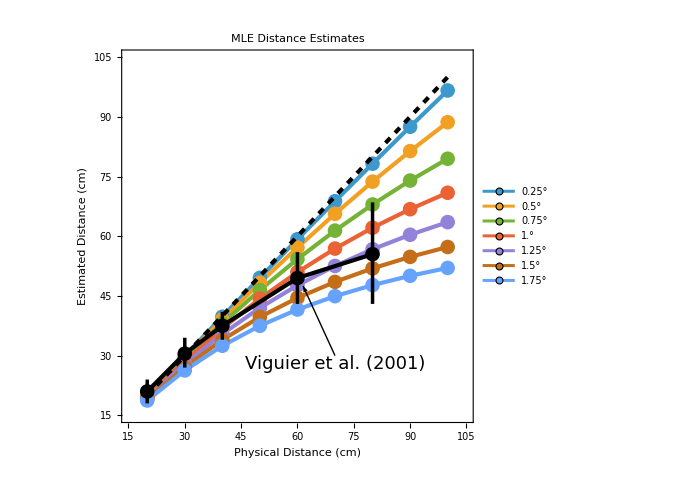

```mathematica
vigCompPlot=Show[ mutliNoisePlot, unityLineVig,vigPlot]
```

```mathematica
If[doSaving,Export[StringJoin[NotebookDirectory[],"vigCompPlot.jpg"],vigCompPlot, RasterSize->5000,ImageSize->1200]];
```

## Heat-map of distance estimates from the peak of the PDF

### We construct a heat-map of perceived distance compared to physical distance. Each column of the heatmap is a distance PDF.

```mathematica
(* Distances and vergences to create PDF's for *)
minDist=30;
maxDist=100;
distanceValuesFine=N@Range[minDist, maxDist, 0.25];
numDists=Length[distanceValuesFine];
vergValuesFine=ArcTan[hiodValue/distanceValuesFine];
```

### Create tables of the probability distributions, PDFs and CDFs

```mathematica
(* Probability distributions *)
distribTableProbMap=Table[ProbabilityDistribution[distFuncPDF[Part[vergValuesFine, n],sigmaValueRad, hiodValue], {y, 0, distLimit}],{n, 1, numDists}];
```

```mathematica
(* PDF's *)
distribTableMap=ParallelTable[Simplify[PDF[distribTableProbMap[[n]],y],y>0],{n, 1, numDists}];
```

```mathematica
(* CDF's *)
distribTableMapCDF=ParallelTable[Simplify[CDF[distribTableProbMap[[n]], y],y>0],{n, 1, numDists}];
```

```mathematica
(* Range over which to do the PDF *)
numDistsPDF=500;
maxDistPDF=140;
minDistPDF=0;
xDistRange=N@Subdivide[minDistPDF,maxDistPDF,numDistsPDF];
```

### Plot the PDFs as a grid

```mathematica
(* Make a table of values out of this (use Quiet to get rid of machine precision warnings)  *)
dDistribValues=ParallelTable[Quiet@Table[Part[distribTableMap, n], {y,xDistRange}], {n, 1, Length[distanceValuesFine]}];
```

```mathematica
(* We now have a grid of numbers for our evalued PDFs. We take the maximum and minimum  *)
dDistribValues//Dimensions
Min[dDistribValues]
Max[dDistribValues]
```

{281,501}

0.

0.0857154

```mathematica
(* The heatmap needs to be transposed to get it in the correct orientation for ArrayPlot  *)
finalHeatmap=Transpose@dDistribValues;
```

```mathematica
(* Assign tick labels  *)
numTicks=7;
xticks=Transpose[{Subdivide[1,numDists,numTicks],Subdivide[minDist, maxDist,numTicks]}];
yticks=Transpose[{Subdivide[1,numDistsPDF,numTicks],Subdivide[minDistPDF,maxDistPDF,numTicks]}];
```

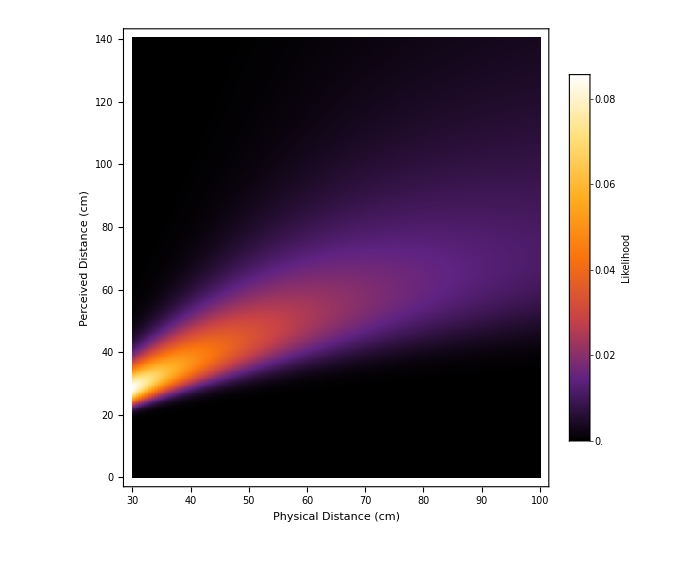

```mathematica
heatMap=ArrayPlot[finalHeatmap,ColorFunction->"SunsetColors",ImageSize->Large, AspectRatio->1, FrameLabel->{{Style["Physical Distance (cm)", frameFS],Style["Probability Density", titleFS]},{Style["Perceived Distance (cm)", frameFS],}}, 
DataReversed->True, Frame-> True, FrameTicks-> {yticks,xticks,None,None}, FrameStyle->Directive[Black,frameFS,Thickness[0.0024]],PlotLegends->{BarLegend[Automatic,Automatic,LegendLabel->"Likelihood",LabelStyle->Directive[Black,FontSize->18],LegendMarkerSize->500,Method->{TicksStyle->{Black,AbsoluteThickness[1]},FrameStyle->{Black,AbsoluteThickness[1]}}]}]
```

## Heat-map of distance estimates from the peak

#### Point estimates of the distributions

```mathematica
(* Peaks *)
thePeakListMap=ParallelTable[FindMaximum[Part[distribTableMap,n], {y, Part[distanceValuesFine, n]}, Method-> "ConjugateGradient"], {n,Length[vergValuesFine]}];
thePeakPosListMap=Part[thePeakListMap, All, 2, 1,2];
```

```mathematica
(* Expectations *)
theExpectPosListMap=ParallelTable[NExpectation[y\[Conditioned]lowerDistLimit<=y<=upperDistLimit,y\[Distributed]distribTableProbMap[[n]]],{n, 1, Length[vergValuesFine]}];
```

```mathematica
(* Medians) *)
theMedianListMap=N[Table[Reduce[Rationalize[distribTableMapCDF[[n]],0]==1/2&&y>0,y,Reals],{n,1,Length[vergValuesFine]}][[All,2]]];
```

Next we need to rescale the points estimates to be consistent with the coordinate frame of the plot

```mathematica
(* Distance for the x-axis *)
distBins=Rescale[distanceValuesFine,{minDistPDF,maxDistPDF},{1,numDistsPDF-1}];
```

```mathematica
(* Rescaled Peaks *)
peakBins=Rescale[thePeakPosListMap,{minDistPDF,maxDistPDF},{1,numDistsPDF-1}];
```

```mathematica
(* Rescaled Expectations *)
expectBins=Rescale[theExpectPosListMap,{minDistPDF,maxDistPDF},{1,numDistsPDF-1}];
```

```mathematica
(* Rescaled Medians *)
medianBins=Rescale[theMedianListMap,{minDistPDF,maxDistPDF},{1,numDistsPDF-1}];
```

Make into x-y pairs for plotting and then graphics

```mathematica
(* Paired X and Y coordinates *)
xValuePeak=Range[0, Length[distanceValuesFine]-1,1]+0.5;
lineCoordsPeaks=Transpose[{xValuePeak,peakBins}];
lineCoordsExpects=Transpose[{xValuePeak,expectBins}];
lineCoordsDist=Transpose[{xValuePeak,distBins}];
lineCoordsMedian=Transpose[{xValuePeak,medianBins}];
```

```mathematica
(* The lines *)
theLinePeaks=Graphics[{Thick,Blue,Line[lineCoordsPeaks]}];
theLineExpects=Graphics[{Thick,Green,Line[lineCoordsExpects]}];
theLineMedians=Graphics[{Thick,Red,Line[lineCoordsMedian]}];
theLineDist=Graphics[{Thick,Dashed,LightGray,Line[lineCoordsDist]}];
```

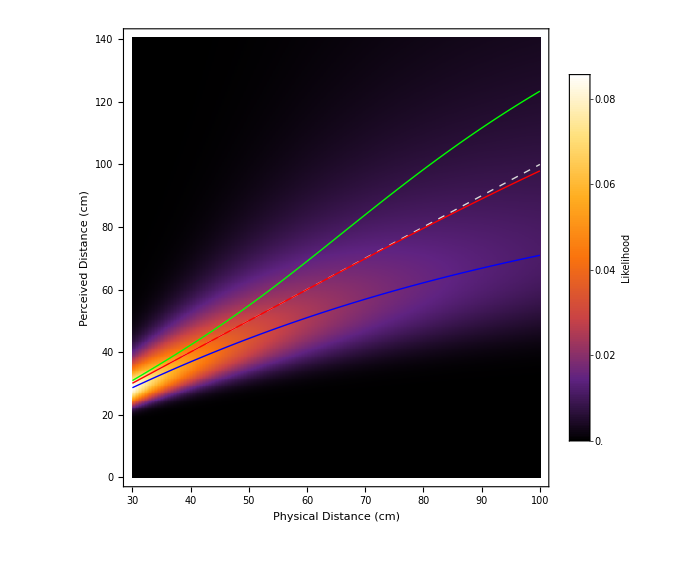

```mathematica
(* Show everything *)
heatmap=Show[heatMap,theLineDist, theLinePeaks,theLineExpects,theLineMedians]
```

```mathematica
If[doSaving,Export[StringJoin[NotebookDirectory[],"BayesHeatmap.jpg"],heatmap,  RasterSize->5000,ImageSize->1200]];
```